# Running PyFrac from mma

## Set-up

First you must make sure that your pyhton installed can be seen by mma
from workflow/ConfigurePythonForExternalEvaluate
note you must do  at the command line:
$ pip install --user pyzmq

after run  FindExternalEvaluators[“Python”] to see if mma finds your python 

Note that for anaconda, I had to manually register Python as follow
(You did this once - and then it’s fine for subsequent kernel restart) 

SetEnvironment["PATH"→ Environment["PATH"]<>";"<>"/opt/anaconda3/bin"]

SetEnvironment["PATH"→ Environment["PATH"]<>";"<>"/opt/anaconda3/lib/python3.7/site-packages"]

RegisterExternalEvaluator["Python","/opt/anaconda3/bin/python3.7"]

```mathematica
FindExternalEvaluators["Python"]
```

all is good - we are set up ... not quite as mma ExternalEvaluate does not know about PYTHONPATH (not sure why - i guess related to shell - anyone - it’s easy to actually define the path directly during a python session that’s what we will do....

(Note in the notebook - you can click on + and go to External Input for the cell type and you are in python

# checking PYTHONPATH
import os
try:
	user_paths = os.environ['PYTHONPATH'].split(os.pathsep)
except KeyError:
	user_paths = []

user_paths

{}

import sys
sys.path
PyFracPath="/Users/amoeri/Documents/PyFrac_Programms/PyFrac/src"  # replace with your PyFrac src path
sys.path.insert(0,PyFracPath)

sys.path

{/Users/amoeri/Documents/PyFrac_Programms/PyFrac/src,/Applications/Mathematica.app/Contents/SystemFiles/Components/WolframClientForPython,/Applications/Mathematica.app/Contents/SystemFiles/Components/ExternalEvaluate_Python/Resources,/opt/anaconda3/lib/python37.zip,/opt/anaconda3/lib/python3.7,/opt/anaconda3/lib/python3.7/lib-dynload,/Users/amoeri/.local/lib/python3.7/site-packages,/opt/anaconda3/lib/python3.7/site-packages,/opt/anaconda3/lib/python3.7/site-packages/aeosa}

## Running PyFrac

from visualization import *

# loading simulation results
Fr_list, properties = load_fractures(address="/Users/amoeri/Documents/PyFrac_Programms/PyFrac/my_examples/Data/Dikes_Q0",
								sim_name="DI_148")

time_srs = get_fracture_variable(Fr_list,
                                 'time')

time_srs = get_fracture_variable(Fr_list,
                                 'time')
                                 
time_srs

{1.×10^-23,1.0801×10^-23,1.1666×10^-23,1.26002×10^-23,1.36092×10^-23,1.46989×10^-23,1.58758×10^-23,1.71468×10^-23,1.85195×10^-23,2.0002×10^-23,2.16031×10^-23,2.33323×10^-23,2.51426×10^-23,2.70198×10^-23,2.89707×10^-23,3.10022×10^-23,3.31076×10^-23,3.52977×10^-23,3.75623×10^-23,3.99121×10^-23,4.18499×10^-23,4.51699×10^-23,4.87556×10^-23,5.26259×10^-23,5.66321×10^-23,6.07817×10^-23,6.50015×10^-23,6.93961×10^-23,7.398×10^-23,7.87632×10^-23,8.3728×10^-23,8.77716×10^-23,9.46997×10^-23,1.02182×10^-22,1.1021×10^-22,1.18555×10^-22,1.27306×10^-22,1.3633×10^-22,1.45709×10^-22,1.55494×10^-22,1.65604×10^-22,1.76052×10^-22,1.84522×10^-22,1.99034×10^-22,2.14707×10^-22,2.31633×10^-22,2.494×10^-22,2.67948×10^-22,2.8718×10^-22,3.07097×10^-22,3.27703×10^-22,3.49044×10^-22,3.71264×10^-22,3.94197×10^-22,4.13137×10^-22,4.45586×10^-22,4.80632×10^-22,5.18271×10^-22,5.57109×10^-22,5.97381×10^-22,6.39177×10^-22,6.82844×10^-22,7.28033×10^-22,7.74778×10^-22,8.23101×10^-22,8.62716×10^-22,9.30589×10^-22,1.00389×10^-21,1.08306×10^-21,1.16527×10^-21,1.25071×10^-21,1.3398×10^-21,1.43165×10^-21,1.52507×10^-21,1.62252×10^-21,1.72377×10^-21,1.8066×10^-21,1.94852×10^-21,2.10178×10^-21,2.26731×10^-21,2.44141×10^-21,2.6245×10^-21,2.81042×10^-21,3.00442×10^-21,3.20516×10^-21,3.41216×10^-21,3.62726×10^-21,3.80154×10^-21,4.10015×10^-21,4.42265×10^-21,4.77095×10^-21,5.13768×10^-21,5.51823×10^-21,5.91272×10^-21,6.32172×10^-21,6.74731×10^-21,7.18811×10^-21,7.64448×10^-21,8.11633×10^-21,8.50639×10^-21,9.17468×10^-21,9.89643×10^-21,1.0672×10^-20,1.14807×10^-20,1.23168×10^-20,1.31796×10^-20,1.40742×10^-20,1.49989×10^-20,1.59571×10^-20,1.69489×10^-20,1.77652×10^-20,1.91637×10^-20,2.06742×10^-20,2.23055×10^-20,2.39981×10^-20,2.57563×10^-20,2.75929×10^-20,2.94888×10^-20,3.14519×10^-20,3.3475×10^-20,3.55653×10^-20,3.72766×10^-20,4.02086×10^-20,4.33751×10^-20,4.67949×10^-20,5.03883×10^-20,5.41×10^-20,5.7951×10^-20,6.19717×10^-20,6.61305×10^-20,7.04215×10^-20,7.48766×10^-20,7.84767×10^-20,8.46447×10^-20,9.13062×10^-20,9.85006×10^-20,1.06082×10^-19,1.13944×10^-19,1.22093×10^-19,1.3054×10^-19,1.39334×10^-19,1.48441×10^-19,1.5787×10^-19,1.67619×10^-19,1.75677×10^-19,1.89484×10^-19,2.04395×10^-19,2.2042×10^-19,2.37129×10^-19,2.54389×10^-19,2.72218×10^-19,2.90705×10^-19,3.09815×10^-19,3.29615×10^-19,3.50109×10^-19,3.66974×10^-19,3.9587×10^-19,4.27078×10^-19,4.60782×10^-19,4.95756×10^-19,5.32084×10^-19,5.70038×10^-19,6.09213×10^-19,6.49778×10^-19,6.9158×10^-19,7.34773×10^-19,7.70113×10^-19,8.30663×10^-19,8.96057×10^-19,9.66682×10^-19,1.04096×10^-18,1.11913×10^-18,1.1984×10^-18,1.28116×10^-18,1.36674×10^-18,1.45501×10^-18,1.54678×10^-18,1.62114×10^-18,1.74855×10^-18,1.88616×10^-18,2.03477×10^-18,2.19126×10^-18,2.35353×10^-18,2.52179×10^-18,2.69509×10^-18,2.87671×10^-18,3.06594×10^-18,3.26077×10^-18,3.462×10^-18,3.62845×10^-18,3.91362×10^-18,4.22161×10^-18,4.55313×10^-18,4.89728×10^-18,5.25194×10^-18,5.61875×10^-18,5.99974×10^-18,6.39381×10^-18,6.80269×10^-18,7.22974×10^-18,7.57806×10^-18,8.17484×10^-18,8.81938×10^-18,9.51547×10^-18,1.02381×10^-17,1.09886×10^-17,1.17724×10^-17,1.25806×10^-17,1.34182×10^-17,1.42813×10^-17,1.51731×10^-17,1.59034×10^-17,1.71547×10^-17,1.8506×10^-17,1.99655×10^-17,2.15009×10^-17,2.31203×10^-17,2.47586×10^-17,2.64684×10^-17,2.82378×10^-17,3.00631×10^-17,3.19606×10^-17,3.34976×10^-17,3.6131×10^-17,3.89751×10^-17,4.20468×10^-17,4.5283×10^-17,4.86388×10^-17,5.2118×10^-17,5.57245×10^-17,5.94771×10^-17,6.33841×10^-17,6.7415×10^-17,7.15755×10^-17,7.5017×10^-17,8.09135×10^-17,8.72818×10^-17,9.41371×10^-17,1.01259×10^-16,1.08594×10^-16,1.1618×10^-16,1.24059×10^-16,1.32209×10^-16,1.40653×10^-16,1.49489×10^-16,1.56689×10^-16,1.69024×10^-16,1.82346×10^-16,1.96734×10^-16,2.11664×10^-16,2.27184×10^-16,2.43351×10^-16,2.60009×10^-16,2.77188×10^-16,2.94966×10^-16,3.13352×10^-16,3.28432×10^-16,3.54268×10^-16,3.82172×10^-16,4.12308×10^-16,4.44106×10^-16,4.76718×10^-16,5.10636×10^-16,5.45912×10^-16,5.82629×10^-16,6.21133×10^-16,6.60528×10^-16,6.923×10^-16,7.46736×10^-16,8.05527×10^-16,8.69021×10^-16,9.35841×10^-16,1.00514×10^-15,1.07703×10^-15,1.15156×10^-15,1.22914×10^-15,1.30991×10^-15,1.39325×10^-15,1.47978×10^-15,1.55095×10^-15,1.67288×10^-15,1.80457×10^-15,1.94679×10^-15,2.09401×10^-15,2.24593×10^-15,2.40294×10^-15,2.56602×10^-15,2.73471×10^-15,2.90978×10^-15,3.09266×10^-15,3.24169×10^-15,3.49703×10^-15,3.77279×10^-15,4.07061×10^-15,4.38023×10^-15,4.70323×10^-15,5.0395×10^-15,5.3861×10^-15,5.74522×10^-15,6.11528×10^-15,6.49774×10^-15,6.8105×10^-15,7.34637×10^-15,7.92511×10^-15,8.55015×10^-15,9.2041×10^-15,9.90086×10^-15,1.06064×10^-14,1.13422×10^-14,1.21034×10^-14,1.28884×10^-14,1.37043×10^-14,1.43633×10^-14,1.54923×10^-14,1.67117×10^-14,1.80287×10^-14,1.94185×10^-14,2.086×10^-14,2.23547×10^-14,2.39045×10^-14,2.55176×10^-14,2.71978×10^-14,2.89327×10^-14,3.07316×10^-14,3.2209×10^-14,3.47404×10^-14,3.74742×10^-14,4.0423×10^-14,4.34866×10^-14,4.66452×10^-14,4.99094×10^-14,5.33003×10^-14,5.68086×10^-14,6.04505×10^-14,6.42555×10^-14,6.73509×10^-14,7.26543×10^-14,7.83821×10^-14,8.4568×10^-14,9.10149×10^-14,9.77381×10^-14,1.04717×10^-13,1.11924×10^-13,1.19415×10^-13,1.27092×10^-13,1.35031×10^-13,1.41526×10^-13,1.52654×10^-13,1.64672×10^-13,1.77651×10^-13,1.91354×10^-13,2.05505×10^-13,2.20227×10^-13,2.35554×10^-13,2.5142×10^-13,2.68097×10^-13,2.85181×10^-13,2.98887×10^-13,3.22372×10^-13,3.47735×10^-13,3.75127×10^-13,4.03988×10^-13,4.34033×10^-13,4.65207×10^-13,4.97853×10^-13,5.31579×10^-13,5.66568×10^-13,6.02765×10^-13,6.40391×10^-13,6.71182×10^-13,7.23936×10^-13,7.80911×10^-13,8.42443×10^-13,9.06432×10^-13,9.72262×10^-13,1.03973×10^-12,1.11015×10^-12,1.18371×10^-12,1.26043×10^-12,1.33985×10^-12,1.40406×10^-12,1.51408×10^-12,1.6329×10^-12,1.76123×10^-12,1.89713×10^-12,2.03707×10^-12,2.18234×10^-12,2.33353×10^-12,2.49061×10^-12,2.65332×10^-12,2.82096×10^-12,2.9562×10^-12,3.1879×10^-12,3.43814×10^-12,3.70839×10^-12,3.99651×10^-12,4.29549×10^-12,4.60555×10^-12,4.92736×10^-12,5.26247×10^-12,5.60942×10^-12,5.97102×10^-12,6.34562×10^-12,6.6501×10^-12,7.17178×10^-12,7.73519×10^-12,8.34368×10^-12,8.98019×10^-12,9.64028×10^-12,1.03129×10^-11,1.10151×10^-11,1.17515×10^-11,1.25179×10^-11,1.33116×10^-11,1.39491×10^-11,1.50414×10^-11,1.62211×10^-11,1.74952×10^-11,1.88522×10^-11,2.02531×10^-11,2.17109×10^-11,2.32327×10^-11,2.48072×10^-11,2.64392×10^-11,2.8138×10^-11,2.94862×10^-11,3.17961×10^-11,3.42908×10^-11,3.69851×10^-11,3.98785×10^-11,4.28829×10^-11,4.60094×10^-11,4.92754×10^-11,5.26629×10^-11,5.6183×10^-11,5.98308×10^-11,6.36199×10^-11,6.66725×10^-11,7.19026×10^-11,7.75512×10^-11,8.36516×10^-11,9.00978×10^-11,9.6837×10^-11,1.03859×10^-10,1.11023×10^-10,1.18453×10^-10,1.26197×10^-10,1.34258×10^-10,1.40691×10^-10,1.51713×10^-10,1.63617×10^-10,1.76472×10^-10,1.90357×10^-10,2.04878×10^-10,2.19988×10^-10,2.35627×10^-10,2.51887×10^-10,2.68734×10^-10,2.86298×10^-10,2.99978×10^-10,3.23418×10^-10,3.48732×10^-10,3.76072×10^-10,4.05599×10^-10,4.36702×10^-10,4.69068×10^-10,5.02753×10^-10,5.38108×10^-10,5.74819×10^-10,6.1267×10^-10,6.52256×10^-10,6.83528×10^-10,7.37107×10^-10,7.94972×10^-10,8.57467×10^-10,9.24441×10^-10,9.95237×10^-10,1.0687×10^-9,1.14505×10^-9,1.22387×10^-9,1.30686×10^-9,1.39341×10^-9,1.46006×10^-9,1.57424×10^-9,1.69756×10^-9,1.83075×10^-9,1.9746×10^-9,2.12871×10^-9,2.28933×10^-9,2.45836×10^-9,2.63305×10^-9,2.813×10^-9,2.99909×10^-9,3.1931×10^-9,3.3459×10^-9,3.6077×10^-9,3.89044×10^-9,4.1958×10^-9,4.52558×10^-9,4.87592×10^-9,5.2399×10^-9,5.61713×10^-9,6.00736×10^-9,6.41791×10^-9,6.84761×10^-9,7.17481×10^-9,7.73541×10^-9,8.34086×10^-9,8.99474×10^-9,9.70093×10^-9,1.04484×10^-8,1.1239×10^-8,1.20642×10^-8,1.29209×10^-8,1.38136×10^-8,1.47465×10^-8,1.57318×10^-8,1.64863×10^-8,1.77788×10^-8,1.91748×10^-8,2.06825×10^-8,2.23107×10^-8,2.40646×10^-8,2.58927×10^-8,2.77757×10^-8,2.97775×10^-8,3.186×10^-8,3.40134×10^-8,3.62191×10^-8,3.79516×10^-8,4.092×10^-8,4.41258×10^-8,4.75881×10^-8,5.13274×10^-8,5.5349×10^-8,5.95221×10^-8,6.38496×10^-8,6.83586×10^-8,7.31277×10^-8,7.81314×10^-8,8.18606×10^-8,8.82498×10^-8,9.51502×10^-8,1.02603×10^-7,1.10651×10^-7,1.19344×10^-7,1.28503×10^-7,1.3809×10^-7,1.48102×10^-7,1.58527×10^-7,1.69545×10^-7,1.81019×10^-7,1.89649×10^-7,2.04435×10^-7,2.20404×10^-7,2.3765×10^-7,2.56276×10^-7,2.76392×10^-7,2.97588×10^-7,3.19983×10^-7,3.43314×10^-7,3.67463×10^-7,3.92147×10^-7,4.18787×10^-7,4.38817×10^-7,4.73137×10^-7,5.10201×10^-7,5.50231×10^-7,5.93464×10^-7,6.40155×10^-7,6.8925×10^-7,7.40598×10^-7,7.94924×10^-7,8.51045×10^-7,9.08817×10^-7,9.69987×10^-7,1.0164×10^-6,1.09593×10^-6,1.18181×10^-6,1.27457×10^-6,1.37475×10^-6,1.48294×10^-6,1.59682×10^-6,1.71493×10^-6,1.84111×10^-6,1.97202×10^-6,2.10602×10^-6,2.24407×10^-6,2.35129×10^-6,2.53499×10^-6,2.73339×10^-6,2.94765×10^-6,3.17906×10^-6,3.42777×10^-6,3.68879×10^-6,3.95781×10^-6,4.24871×10^-6,4.55255×10^-6,4.86308×10^-6,5.18153×10^-6,5.42881×10^-6,5.85249×10^-6,6.31007×10^-6,6.80424×10^-6,7.33796×10^-6,7.9104×10^-6,8.51316×10^-6,9.13747×10^-6,9.80993×10^-6,0.0000105119,0.0000112276,0.0000119673,0.0000125382,0.0000135163,0.0000145726,0.0000156051,0.0000168285,0.0000181498,0.0000195315,0.0000209866,0.0000225475,0.0000241553,0.0000257909,0.0000275178,0.0000288319,0.0000310835,0.0000335153,0.0000361416,0.0000389779,0.0000420412,0.0000452587,0.0000486488,0.0000522523,0.0000559808,0.0000597767,0.0000637489,0.000066793,0.0000720087,0.0000776415,0.000083725,0.0000902952,0.000097391,0.000104842,0.000112693,0.000121054,0.000129651,0.000138365,0.000147511,0.000154555,0.000166625,0.000179659,0.000193737,0.000208941,0.000225361,0.000242603,0.000260812,0.000280178,0.000300077,0.000320223,0.000341827,0.000358151,0.000386119,0.000416324,0.000448358,0.000483542,0.000520619,0.000559831,0.000600886,0.000644637,0.000691222,0.00073909,0.000787422,0.000825022,0.000889443,0.000959019,0.00103416,0.00111531,0.0012006,0.0012911,0.00138702,0.0014883,0.00159353,0.00170212,0.00181412,0.00190083,0.00204938,0.00220982,0.00238309,0.00257022,0.00277233,0.00298455,0.00321054,0.00344711,0.00369295,0.0039427,0.00421725,0.00441872,0.00476389,0.00513668,0.00553929,0.00597029,0.00642153,0.00691377,0.00742584,0.00797712,0.00853925,0.00911278,0.00971167,0.010176,0.0109714,0.0118306,0.0127584,0.0137605,0.0148427,0.015973,0.0171721,0.018403,0.019673,0.02099,0.0223385,0.0234058,0.0252344,0.0272092,0.0293421,0.0316456,0.034064,0.0366726,0.039362,0.0421948,0.0451282,0.0482009,0.0512891,0.0537346,0.0579245,0.0624495,0.0673366,0.0722265,0.0774484,0.083001,0.0888127,0.0947569,0.101059,0.107637,0.114387,0.121414,0.1272,0.137114,0.147821,0.159278,0.170844,0.182794,0.195071,0.207798,0.221121,0.234811,0.24919,0.263698,0.278599,0.291854,0.314565,0.339092,0.36364,0.388569,0.413865,0.438945,0.464632,0.491859,0.522663,0.55365,0.584663,0.615777,0.647084,0.677905,0.727074,0.783815,0.835221,0.886124,0.937765,0.992218,1.04687,1.1011,1.15743,1.21549,1.27479,1.3335,1.39488,1.45716,1.52001,1.59236,1.71589,1.82645,1.93484,2.03463,2.13461,2.2428,2.35599,2.4689,2.5815,2.69622,2.81338,2.9325,3.04866,3.16533,3.28693,3.41248,3.53869,3.70758,3.92144,4.12935,4.33055,4.52338,4.71677,4.91351,5.11539,5.32117,5.53332,5.7622,5.99403,6.21352,6.4315,6.65542,6.88038,7.10948,7.33378,7.55994,7.79482,8.03525,8.3723,8.74628,9.1821,9.62027,10.0409,10.461,10.8785,11.2962,11.7525,12.223,12.6932,13.1506,13.6366,14.1247,14.6164,15.096,15.5766,16.0754,16.5782,17.0878,17.5995,18.1535,18.7142,19.2584,19.9982,21.1422,22.259,23.2529,24.188,25.1265,26.0739,27.0666,28.0725,29.1147,30.177,31.2406,32.28,33.2842,34.3158,35.3361,36.3555,37.3626,38.4113,39.4931,40.5931,41.6794,42.7694,43.9132,45.0805,46.3115,47.5489,48.8136,50.6182,53.5395,56.0757,58.5614,60.8784,63.0474,65.2526,67.4728,69.6841,71.881,73.9927,76.1529,78.3044,80.4614,82.5809,84.6303,86.7406,88.987,91.2748,93.5299,95.7622,98.0807,100.454,102.862,105.272,107.843,110.508,113.213,115.892,118.587,122.506,127.166,132.376,137.416,142.274,147.021,151.831,156.662,161.489,166.083,170.622,175.298,179.821,183.885,187.787,191.564,195.381,199.383,203.745,208.218,212.663,217.708,222.863,227.956,232.834,237.948,243.139,248.346,253.401,258.487,263.768,269.069,274.399,279.693,284.971,290.396,295.734,300.992,306.118,311.237,316.416,321.57,328.762,338.904,349.053,359.313,368.989,378.586,387.831,396.756,405.478,414.3,422.809,431.171,438.642,445.689,452.797,459.861,466.873,473.411,479.948,487.242,495.252,503.475,511.679,520.148,529.119,538.248,547.132,555.841,564.753,573.467,581.576,589.567,597.499,605.572,613.658,621.644,629.026,636.417,643.996,651.639,659.194,666.585,674.417,682.445,690.561,698.515,706.274,714.313,722.342,730.261,737.938,744.896,751.936,758.998,766.016,772.706,779.376,786.241,793.46,800.833,808.085,815.261,822.692,830.149,837.497,844.616,851.723,858.968,866.114,873.121,879.883,886.568,893.322,899.96,906.308,912.49,918.541,924.669,930.743,936.741,942.412,948.029,953.811,959.536,965.241,970.784,976.227,981.787,987.271,992.67,997.893,1000.,1004.21,1008.82,1013.61,1018.92,1024.44,1030.02,1036.24,1043.53,1051.34,1059.9,1070.59,1083.24,1098.07,1127.73,1177.94,1234.32,1302.74,1381.62,1467.11,1564.05,1719.59,1975.77,2272.14,2612.96,3004.9,3455.64,3973.98,4570.08,5255.59,6043.93,6950.52,7993.1,9192.06,10570.9,12156.5,13980.,16077.,18488.5,21261.8,24451.1,28118.7,32336.5,37187.,42765.1,49179.8,56556.8,65040.3,74796.4,86015.8,98918.2,113756.,130819.,150442.,173009.,198960.,228804.,263124.,302593.,347982.,400179.,460206.,529237.,608623.,699916.,804903.,925639.,1.06448×10^6,1.22416×10^6,1.40778×10^6,1.61895×10^6,1.86179×10^6,2.14106×10^6,2.46222×10^6,2.83155×10^6,3.25628×10^6,3.74473×10^6,4.30643×10^6,4.9524×10^6,5.69526×10^6,6.54955×10^6,7.53198×10^6,8.66178×10^6,9.96104×10^6,1.14552×10^7,1.31735×10^7,1.51495×10^7,1.74219×10^7,2.00352×10^7,2.30405×10^7,2.64966×10^7,3.04711×10^7,3.50417×10^7,4.0298×10^7,4.63427×10^7,5.19038×10^7,5.96894×10^7,6.86428×10^7,7.89392×10^7,9.07801×10^7,1.04397×10^8,1.20057×10^8,1.38065×10^8,1.58775×10^8,1.82591×10^8,2.0998×10^8,2.41477×10^8,2.77698×10^8,3.19353×10^8,3.67256×10^8,4.22344×10^8,4.85696×10^8,5.5855×10^8,6.42333×10^8,7.38683×10^8,8.49485×10^8,9.76908×10^8,1.12344×10^9,1.29196×10^9,1.48576×10^9,1.70862×10^9,1.96491×10^9,2.25965×10^9,2.5986×10^9,2.98838×10^9,3.43664×10^9,3.95214×10^9,4.54496×10^9,5.2267×10^9}

```mathematica
t=%
```

{1.×10^-23,1.0801×10^-23,1.1666×10^-23,1.26002×10^-23,1.36092×10^-23,1.46989×10^-23,1.58758×10^-23,1.71468×10^-23,1.85195×10^-23,2.0002×10^-23,2.16031×10^-23,2.33323×10^-23,2.51426×10^-23,2.70198×10^-23,2.89707×10^-23,3.10022×10^-23,3.31076×10^-23,3.52977×10^-23,3.75623×10^-23,3.99121×10^-23,4.18499×10^-23,4.51699×10^-23,4.87556×10^-23,5.26259×10^-23,5.66321×10^-23,6.07817×10^-23,6.50015×10^-23,6.93961×10^-23,7.398×10^-23,7.87632×10^-23,8.3728×10^-23,8.77716×10^-23,9.46997×10^-23,1.02182×10^-22,1.1021×10^-22,1.18555×10^-22,1.27306×10^-22,1.3633×10^-22,1.45709×10^-22,1.55494×10^-22,1.65604×10^-22,1.76052×10^-22,1.84522×10^-22,1.99034×10^-22,2.14707×10^-22,2.31633×10^-22,2.494×10^-22,2.67948×10^-22,2.8718×10^-22,3.07097×10^-22,3.27703×10^-22,3.49044×10^-22,3.71264×10^-22,3.94197×10^-22,4.13137×10^-22,4.45586×10^-22,4.80632×10^-22,5.18271×10^-22,5.57109×10^-22,5.97381×10^-22,6.39177×10^-22,6.82844×10^-22,7.28033×10^-22,7.74778×10^-22,8.23101×10^-22,8.62716×10^-22,9.30589×10^-22,1.00389×10^-21,1.08306×10^-21,1.16527×10^-21,1.25071×10^-21,1.3398×10^-21,1.43165×10^-21,1.52507×10^-21,1.62252×10^-21,1.72377×10^-21,1.8066×10^-21,1.94852×10^-21,2.10178×10^-21,2.26731×10^-21,2.44141×10^-21,2.6245×10^-21,2.81042×10^-21,3.00442×10^-21,3.20516×10^-21,3.41216×10^-21,3.62726×10^-21,3.80154×10^-21,4.10015×10^-21,4.42265×10^-21,4.77095×10^-21,5.13768×10^-21,5.51823×10^-21,5.91272×10^-21,6.32172×10^-21,6.74731×10^-21,7.18811×10^-21,7.64448×10^-21,8.11633×10^-21,8.50639×10^-21,9.17468×10^-21,9.89643×10^-21,1.0672×10^-20,1.14807×10^-20,1.23168×10^-20,1.31796×10^-20,1.40742×10^-20,1.49989×10^-20,1.59571×10^-20,1.69489×10^-20,1.77652×10^-20,1.91637×10^-20,2.06742×10^-20,2.23055×10^-20,2.39981×10^-20,2.57563×10^-20,2.75929×10^-20,2.94888×10^-20,3.14519×10^-20,3.3475×10^-20,3.55653×10^-20,3.72766×10^-20,4.02086×10^-20,4.33751×10^-20,4.67949×10^-20,5.03883×10^-20,5.41×10^-20,5.7951×10^-20,6.19717×10^-20,6.61305×10^-20,7.04215×10^-20,7.48766×10^-20,7.84767×10^-20,8.46447×10^-20,9.13062×10^-20,9.85006×10^-20,1.06082×10^-19,1.13944×10^-19,1.22093×10^-19,1.3054×10^-19,1.39334×10^-19,1.48441×10^-19,1.5787×10^-19,1.67619×10^-19,1.75677×10^-19,1.89484×10^-19,2.04395×10^-19,2.2042×10^-19,2.37129×10^-19,2.54389×10^-19,2.72218×10^-19,2.90705×10^-19,3.09815×10^-19,3.29615×10^-19,3.50109×10^-19,3.66974×10^-19,3.9587×10^-19,4.27078×10^-19,4.60782×10^-19,4.95756×10^-19,5.32084×10^-19,5.70038×10^-19,6.09213×10^-19,6.49778×10^-19,6.9158×10^-19,7.34773×10^-19,7.70113×10^-19,8.30663×10^-19,8.96057×10^-19,9.66682×10^-19,1.04096×10^-18,1.11913×10^-18,1.1984×10^-18,1.28116×10^-18,1.36674×10^-18,1.45501×10^-18,1.54678×10^-18,1.62114×10^-18,1.74855×10^-18,1.88616×10^-18,2.03477×10^-18,2.19126×10^-18,2.35353×10^-18,2.52179×10^-18,2.69509×10^-18,2.87671×10^-18,3.06594×10^-18,3.26077×10^-18,3.462×10^-18,3.62845×10^-18,3.91362×10^-18,4.22161×10^-18,4.55313×10^-18,4.89728×10^-18,5.25194×10^-18,5.61875×10^-18,5.99974×10^-18,6.39381×10^-18,6.80269×10^-18,7.22974×10^-18,7.57806×10^-18,8.17484×10^-18,8.81938×10^-18,9.51547×10^-18,1.02381×10^-17,1.09886×10^-17,1.17724×10^-17,1.25806×10^-17,1.34182×10^-17,1.42813×10^-17,1.51731×10^-17,1.59034×10^-17,1.71547×10^-17,1.8506×10^-17,1.99655×10^-17,2.15009×10^-17,2.31203×10^-17,2.47586×10^-17,2.64684×10^-17,2.82378×10^-17,3.00631×10^-17,3.19606×10^-17,3.34976×10^-17,3.6131×10^-17,3.89751×10^-17,4.20468×10^-17,4.5283×10^-17,4.86388×10^-17,5.2118×10^-17,5.57245×10^-17,5.94771×10^-17,6.33841×10^-17,6.7415×10^-17,7.15755×10^-17,7.5017×10^-17,8.09135×10^-17,8.72818×10^-17,9.41371×10^-17,1.01259×10^-16,1.08594×10^-16,1.1618×10^-16,1.24059×10^-16,1.32209×10^-16,1.40653×10^-16,1.49489×10^-16,1.56689×10^-16,1.69024×10^-16,1.82346×10^-16,1.96734×10^-16,2.11664×10^-16,2.27184×10^-16,2.43351×10^-16,2.60009×10^-16,2.77188×10^-16,2.94966×10^-16,3.13352×10^-16,3.28432×10^-16,3.54268×10^-16,3.82172×10^-16,4.12308×10^-16,4.44106×10^-16,4.76718×10^-16,5.10636×10^-16,5.45912×10^-16,5.82629×10^-16,6.21133×10^-16,6.60528×10^-16,6.923×10^-16,7.46736×10^-16,8.05527×10^-16,8.69021×10^-16,9.35841×10^-16,1.00514×10^-15,1.07703×10^-15,1.15156×10^-15,1.22914×10^-15,1.30991×10^-15,1.39325×10^-15,1.47978×10^-15,1.55095×10^-15,1.67288×10^-15,1.80457×10^-15,1.94679×10^-15,2.09401×10^-15,2.24593×10^-15,2.40294×10^-15,2.56602×10^-15,2.73471×10^-15,2.90978×10^-15,3.09266×10^-15,3.24169×10^-15,3.49703×10^-15,3.77279×10^-15,4.07061×10^-15,4.38023×10^-15,4.70323×10^-15,5.0395×10^-15,5.3861×10^-15,5.74522×10^-15,6.11528×10^-15,6.49774×10^-15,6.8105×10^-15,7.34637×10^-15,7.92511×10^-15,8.55015×10^-15,9.2041×10^-15,9.90086×10^-15,1.06064×10^-14,1.13422×10^-14,1.21034×10^-14,1.28884×10^-14,1.37043×10^-14,1.43633×10^-14,1.54923×10^-14,1.67117×10^-14,1.80287×10^-14,1.94185×10^-14,2.086×10^-14,2.23547×10^-14,2.39045×10^-14,2.55176×10^-14,2.71978×10^-14,2.89327×10^-14,3.07316×10^-14,3.2209×10^-14,3.47404×10^-14,3.74742×10^-14,4.0423×10^-14,4.34866×10^-14,4.66452×10^-14,4.99094×10^-14,5.33003×10^-14,5.68086×10^-14,6.04505×10^-14,6.42555×10^-14,6.73509×10^-14,7.26543×10^-14,7.83821×10^-14,8.4568×10^-14,9.10149×10^-14,9.77381×10^-14,1.04717×10^-13,1.11924×10^-13,1.19415×10^-13,1.27092×10^-13,1.35031×10^-13,1.41526×10^-13,1.52654×10^-13,1.64672×10^-13,1.77651×10^-13,1.91354×10^-13,2.05505×10^-13,2.20227×10^-13,2.35554×10^-13,2.5142×10^-13,2.68097×10^-13,2.85181×10^-13,2.98887×10^-13,3.22372×10^-13,3.47735×10^-13,3.75127×10^-13,4.03988×10^-13,4.34033×10^-13,4.65207×10^-13,4.97853×10^-13,5.31579×10^-13,5.66568×10^-13,6.02765×10^-13,6.40391×10^-13,6.71182×10^-13,7.23936×10^-13,7.80911×10^-13,8.42443×10^-13,9.06432×10^-13,9.72262×10^-13,1.03973×10^-12,1.11015×10^-12,1.18371×10^-12,1.26043×10^-12,1.33985×10^-12,1.40406×10^-12,1.51408×10^-12,1.6329×10^-12,1.76123×10^-12,1.89713×10^-12,2.03707×10^-12,2.18234×10^-12,2.33353×10^-12,2.49061×10^-12,2.65332×10^-12,2.82096×10^-12,2.9562×10^-12,3.1879×10^-12,3.43814×10^-12,3.70839×10^-12,3.99651×10^-12,4.29549×10^-12,4.60555×10^-12,4.92736×10^-12,5.26247×10^-12,5.60942×10^-12,5.97102×10^-12,6.34562×10^-12,6.6501×10^-12,7.17178×10^-12,7.73519×10^-12,8.34368×10^-12,8.98019×10^-12,9.64028×10^-12,1.03129×10^-11,1.10151×10^-11,1.17515×10^-11,1.25179×10^-11,1.33116×10^-11,1.39491×10^-11,1.50414×10^-11,1.62211×10^-11,1.74952×10^-11,1.88522×10^-11,2.02531×10^-11,2.17109×10^-11,2.32327×10^-11,2.48072×10^-11,2.64392×10^-11,2.8138×10^-11,2.94862×10^-11,3.17961×10^-11,3.42908×10^-11,3.69851×10^-11,3.98785×10^-11,4.28829×10^-11,4.60094×10^-11,4.92754×10^-11,5.26629×10^-11,5.6183×10^-11,5.98308×10^-11,6.36199×10^-11,6.66725×10^-11,7.19026×10^-11,7.75512×10^-11,8.36516×10^-11,9.00978×10^-11,9.6837×10^-11,1.03859×10^-10,1.11023×10^-10,1.18453×10^-10,1.26197×10^-10,1.34258×10^-10,1.40691×10^-10,1.51713×10^-10,1.63617×10^-10,1.76472×10^-10,1.90357×10^-10,2.04878×10^-10,2.19988×10^-10,2.35627×10^-10,2.51887×10^-10,2.68734×10^-10,2.86298×10^-10,2.99978×10^-10,3.23418×10^-10,3.48732×10^-10,3.76072×10^-10,4.05599×10^-10,4.36702×10^-10,4.69068×10^-10,5.02753×10^-10,5.38108×10^-10,5.74819×10^-10,6.1267×10^-10,6.52256×10^-10,6.83528×10^-10,7.37107×10^-10,7.94972×10^-10,8.57467×10^-10,9.24441×10^-10,9.95237×10^-10,1.0687×10^-9,1.14505×10^-9,1.22387×10^-9,1.30686×10^-9,1.39341×10^-9,1.46006×10^-9,1.57424×10^-9,1.69756×10^-9,1.83075×10^-9,1.9746×10^-9,2.12871×10^-9,2.28933×10^-9,2.45836×10^-9,2.63305×10^-9,2.813×10^-9,2.99909×10^-9,3.1931×10^-9,3.3459×10^-9,3.6077×10^-9,3.89044×10^-9,4.1958×10^-9,4.52558×10^-9,4.87592×10^-9,5.2399×10^-9,5.61713×10^-9,6.00736×10^-9,6.41791×10^-9,6.84761×10^-9,7.17481×10^-9,7.73541×10^-9,8.34086×10^-9,8.99474×10^-9,9.70093×10^-9,1.04484×10^-8,1.1239×10^-8,1.20642×10^-8,1.29209×10^-8,1.38136×10^-8,1.47465×10^-8,1.57318×10^-8,1.64863×10^-8,1.77788×10^-8,1.91748×10^-8,2.06825×10^-8,2.23107×10^-8,2.40646×10^-8,2.58927×10^-8,2.77757×10^-8,2.97775×10^-8,3.186×10^-8,3.40134×10^-8,3.62191×10^-8,3.79516×10^-8,4.092×10^-8,4.41258×10^-8,4.75881×10^-8,5.13274×10^-8,5.5349×10^-8,5.95221×10^-8,6.38496×10^-8,6.83586×10^-8,7.31277×10^-8,7.81314×10^-8,8.18606×10^-8,8.82498×10^-8,9.51502×10^-8,1.02603×10^-7,1.10651×10^-7,1.19344×10^-7,1.28503×10^-7,1.3809×10^-7,1.48102×10^-7,1.58527×10^-7,1.69545×10^-7,1.81019×10^-7,1.89649×10^-7,2.04435×10^-7,2.20404×10^-7,2.3765×10^-7,2.56276×10^-7,2.76392×10^-7,2.97588×10^-7,3.19983×10^-7,3.43314×10^-7,3.67463×10^-7,3.92147×10^-7,4.18787×10^-7,4.38817×10^-7,4.73137×10^-7,5.10201×10^-7,5.50231×10^-7,5.93464×10^-7,6.40155×10^-7,6.8925×10^-7,7.40598×10^-7,7.94924×10^-7,8.51045×10^-7,9.08817×10^-7,9.69987×10^-7,1.0164×10^-6,1.09593×10^-6,1.18181×10^-6,1.27457×10^-6,1.37475×10^-6,1.48294×10^-6,1.59682×10^-6,1.71493×10^-6,1.84111×10^-6,1.97202×10^-6,2.10602×10^-6,2.24407×10^-6,2.35129×10^-6,2.53499×10^-6,2.73339×10^-6,2.94765×10^-6,3.17906×10^-6,3.42777×10^-6,3.68879×10^-6,3.95781×10^-6,4.24871×10^-6,4.55255×10^-6,4.86308×10^-6,5.18153×10^-6,5.42881×10^-6,5.85249×10^-6,6.31007×10^-6,6.80424×10^-6,7.33796×10^-6,7.9104×10^-6,8.51316×10^-6,9.13747×10^-6,9.80993×10^-6,0.0000105119,0.0000112276,0.0000119673,0.0000125382,0.0000135163,0.0000145726,0.0000156051,0.0000168285,0.0000181498,0.0000195315,0.0000209866,0.0000225475,0.0000241553,0.0000257909,0.0000275178,0.0000288319,0.0000310835,0.0000335153,0.0000361416,0.0000389779,0.0000420412,0.0000452587,0.0000486488,0.0000522523,0.0000559808,0.0000597767,0.0000637489,0.000066793,0.0000720087,0.0000776415,0.000083725,0.0000902952,0.000097391,0.000104842,0.000112693,0.000121054,0.000129651,0.000138365,0.000147511,0.000154555,0.000166625,0.000179659,0.000193737,0.000208941,0.000225361,0.000242603,0.000260812,0.000280178,0.000300077,0.000320223,0.000341827,0.000358151,0.000386119,0.000416324,0.000448358,0.000483542,0.000520619,0.000559831,0.000600886,0.000644637,0.000691222,0.00073909,0.000787422,0.000825022,0.000889443,0.000959019,0.00103416,0.00111531,0.0012006,0.0012911,0.00138702,0.0014883,0.00159353,0.00170212,0.00181412,0.00190083,0.00204938,0.00220982,0.00238309,0.00257022,0.00277233,0.00298455,0.00321054,0.00344711,0.00369295,0.0039427,0.00421725,0.00441872,0.00476389,0.00513668,0.00553929,0.00597029,0.00642153,0.00691377,0.00742584,0.00797712,0.00853925,0.00911278,0.00971167,0.010176,0.0109714,0.0118306,0.0127584,0.0137605,0.0148427,0.015973,0.0171721,0.018403,0.019673,0.02099,0.0223385,0.0234058,0.0252344,0.0272092,0.0293421,0.0316456,0.034064,0.0366726,0.039362,0.0421948,0.0451282,0.0482009,0.0512891,0.0537346,0.0579245,0.0624495,0.0673366,0.0722265,0.0774484,0.083001,0.0888127,0.0947569,0.101059,0.107637,0.114387,0.121414,0.1272,0.137114,0.147821,0.159278,0.170844,0.182794,0.195071,0.207798,0.221121,0.234811,0.24919,0.263698,0.278599,0.291854,0.314565,0.339092,0.36364,0.388569,0.413865,0.438945,0.464632,0.491859,0.522663,0.55365,0.584663,0.615777,0.647084,0.677905,0.727074,0.783815,0.835221,0.886124,0.937765,0.992218,1.04687,1.1011,1.15743,1.21549,1.27479,1.3335,1.39488,1.45716,1.52001,1.59236,1.71589,1.82645,1.93484,2.03463,2.13461,2.2428,2.35599,2.4689,2.5815,2.69622,2.81338,2.9325,3.04866,3.16533,3.28693,3.41248,3.53869,3.70758,3.92144,4.12935,4.33055,4.52338,4.71677,4.91351,5.11539,5.32117,5.53332,5.7622,5.99403,6.21352,6.4315,6.65542,6.88038,7.10948,7.33378,7.55994,7.79482,8.03525,8.3723,8.74628,9.1821,9.62027,10.0409,10.461,10.8785,11.2962,11.7525,12.223,12.6932,13.1506,13.6366,14.1247,14.6164,15.096,15.5766,16.0754,16.5782,17.0878,17.5995,18.1535,18.7142,19.2584,19.9982,21.1422,22.259,23.2529,24.188,25.1265,26.0739,27.0666,28.0725,29.1147,30.177,31.2406,32.28,33.2842,34.3158,35.3361,36.3555,37.3626,38.4113,39.4931,40.5931,41.6794,42.7694,43.9132,45.0805,46.3115,47.5489,48.8136,50.6182,53.5395,56.0757,58.5614,60.8784,63.0474,65.2526,67.4728,69.6841,71.881,73.9927,76.1529,78.3044,80.4614,82.5809,84.6303,86.7406,88.987,91.2748,93.5299,95.7622,98.0807,100.454,102.862,105.272,107.843,110.508,113.213,115.892,118.587,122.506,127.166,132.376,137.416,142.274,147.021,151.831,156.662,161.489,166.083,170.622,175.298,179.821,183.885,187.787,191.564,195.381,199.383,203.745,208.218,212.663,217.708,222.863,227.956,232.834,237.948,243.139,248.346,253.401,258.487,263.768,269.069,274.399,279.693,284.971,290.396,295.734,300.992,306.118,311.237,316.416,321.57,328.762,338.904,349.053,359.313,368.989,378.586,387.831,396.756,405.478,414.3,422.809,431.171,438.642,445.689,452.797,459.861,466.873,473.411,479.948,487.242,495.252,503.475,511.679,520.148,529.119,538.248,547.132,555.841,564.753,573.467,581.576,589.567,597.499,605.572,613.658,621.644,629.026,636.417,643.996,651.639,659.194,666.585,674.417,682.445,690.561,698.515,706.274,714.313,722.342,730.261,737.938,744.896,751.936,758.998,766.016,772.706,779.376,786.241,793.46,800.833,808.085,815.261,822.692,830.149,837.497,844.616,851.723,858.968,866.114,873.121,879.883,886.568,893.322,899.96,906.308,912.49,918.541,924.669,930.743,936.741,942.412,948.029,953.811,959.536,965.241,970.784,976.227,981.787,987.271,992.67,997.893,1000.,1004.21,1008.82,1013.61,1018.92,1024.44,1030.02,1036.24,1043.53,1051.34,1059.9,1070.59,1083.24,1098.07,1127.73,1177.94,1234.32,1302.74,1381.62,1467.11,1564.05,1719.59,1975.77,2272.14,2612.96,3004.9,3455.64,3973.98,4570.08,5255.59,6043.93,6950.52,7993.1,9192.06,10570.9,12156.5,13980.,16077.,18488.5,21261.8,24451.1,28118.7,32336.5,37187.,42765.1,49179.8,56556.8,65040.3,74796.4,86015.8,98918.2,113756.,130819.,150442.,173009.,198960.,228804.,263124.,302593.,347982.,400179.,460206.,529237.,608623.,699916.,804903.,925639.,1.06448×10^6,1.22416×10^6,1.40778×10^6,1.61895×10^6,1.86179×10^6,2.14106×10^6,2.46222×10^6,2.83155×10^6,3.25628×10^6,3.74473×10^6,4.30643×10^6,4.9524×10^6,5.69526×10^6,6.54955×10^6,7.53198×10^6,8.66178×10^6,9.96104×10^6,1.14552×10^7,1.31735×10^7,1.51495×10^7,1.74219×10^7,2.00352×10^7,2.30405×10^7,2.64966×10^7,3.04711×10^7,3.50417×10^7,4.0298×10^7,4.63427×10^7,5.19038×10^7,5.96894×10^7,6.86428×10^7,7.89392×10^7,9.07801×10^7,1.04397×10^8,1.20057×10^8,1.38065×10^8,1.58775×10^8,1.82591×10^8,2.0998×10^8,2.41477×10^8,2.77698×10^8,3.19353×10^8,3.67256×10^8,4.22344×10^8,4.85696×10^8,5.5855×10^8,6.42333×10^8,7.38683×10^8,8.49485×10^8,9.76908×10^8,1.12344×10^9,1.29196×10^9,1.48576×10^9,1.70862×10^9,1.96491×10^9,2.25965×10^9,2.5986×10^9,2.98838×10^9,3.43664×10^9,3.95214×10^9,4.54496×10^9,5.2267×10^9}

frac_eff = get_fracture_variable(Fr_list,
                                 'efficiency')
frac_eff

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
eta=%
```

{1.,0.996996,0.992877,0.990973,0.988878,0.986739,0.984401,0.982397,0.979684,0.976538,0.972827,0.972033}

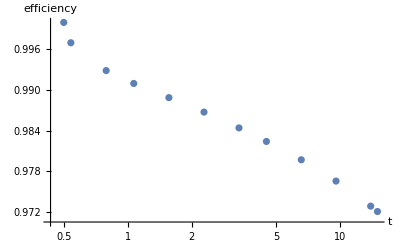

```mathematica
ListLogLinearPlot[Transpose[{t,eta}],AxesLabel->{"t","efficiency"}]
```

frac_r = get_fracture_variable(Fr_list,
                                 'd_mean')
frac_r

{5.11834×10^-8,5.28058×10^-8,5.45249×10^-8,5.63501×10^-8,5.82674×10^-8,6.02497×10^-8,6.23304×10^-8,6.44903×10^-8,6.67389×10^-8,6.90826×10^-8,7.14914×10^-8,7.39769×10^-8,7.65008×10^-8,7.90187×10^-8,8.15333×10^-8,8.40457×10^-8,8.65608×10^-8,8.90965×10^-8,9.16243×10^-8,9.41379×10^-8,9.58696×10^-8,9.90708×10^-8,1.02453×10^-7,1.05991×10^-7,1.09528×10^-7,1.13042×10^-7,1.16519×10^-7,1.20017×10^-7,1.23529×10^-7,1.27049×10^-7,1.30606×10^-7,1.32935×10^-7,1.37381×10^-7,1.42108×10^-7,1.46986×10^-7,1.51846×10^-7,1.56788×10^-7,1.61698×10^-7,1.66627×10^-7,1.71559×10^-7,1.76501×10^-7,1.81466×10^-7,1.84693×10^-7,1.9088×10^-7,1.97418×10^-7,2.04213×10^-7,2.11087×10^-7,2.18018×10^-7,2.2496×10^-7,2.31857×10^-7,2.38761×10^-7,2.45673×10^-7,2.52642×10^-7,2.59564×10^-7,2.6424×10^-7,2.73053×10^-7,2.8238×10^-7,2.9205×10^-7,3.01743×10^-7,3.11389×10^-7,3.20999×10^-7,3.3075×10^-7,3.40506×10^-7,3.50201×10^-7,3.59902×10^-7,3.66625×10^-7,3.78863×10^-7,3.91803×10^-7,4.05377×10^-7,4.18845×10^-7,4.3234×10^-7,4.46025×10^-7,4.59654×10^-7,4.72986×10^-7,4.86473×10^-7,5.00016×10^-7,5.0898×10^-7,5.25978×10^-7,5.43991×10^-7,5.62487×10^-7,5.81066×10^-7,6.00462×10^-7,6.19412×10^-7,6.38541×10^-7,6.57476×10^-7,6.76388×10^-7,6.95415×10^-7,7.07913×10^-7,7.31724×10^-7,7.56868×10^-7,7.82839×10^-7,8.09384×10^-7,8.35904×10^-7,8.62499×10^-7,8.88888×10^-7,9.15461×10^-7,9.42173×10^-7,9.68863×10^-7,9.95382×10^-7,1.01345×10^-6,1.04724×10^-6,1.08301×10^-6,1.12009×10^-6,1.15762×10^-6,1.19469×10^-6,1.23175×10^-6,1.26908×10^-6,1.30636×10^-6,1.34338×10^-6,1.38056×10^-6,1.40633×10^-6,1.45352×10^-6,1.50328×10^-6,1.55543×10^-6,1.60698×10^-6,1.65877×10^-6,1.71121×10^-6,1.76344×10^-6,1.81549×10^-6,1.86754×10^-6,1.91953×10^-6,1.9544×10^-6,2.01992×10^-6,2.08931×10^-6,2.16129×10^-6,2.23377×10^-6,2.3067×10^-6,2.37939×10^-6,2.45291×10^-6,2.52569×10^-6,2.59843×10^-6,2.67159×10^-6,2.71952×10^-6,2.81075×10^-6,2.90709×10^-6,3.00685×10^-6,3.10893×10^-6,3.21083×10^-6,3.31304×10^-6,3.4143×10^-6,3.51641×10^-6,3.61905×10^-6,3.72152×10^-6,3.82344×10^-6,3.89286×10^-6,4.02274×10^-6,4.16017×10^-6,4.30264×10^-6,4.44698×10^-6,4.58923×10^-6,4.7316×10^-6,4.87505×10^-6,5.01826×10^-6,5.16047×10^-6,5.30333×10^-6,5.40229×10^-6,5.58359×10^-6,5.77473×10^-6,5.97508×10^-6,6.17309×10^-6,6.37207×10^-6,6.57353×10^-6,6.77419×10^-6,6.97413×10^-6,7.17409×10^-6,7.37381×10^-6,7.50705×10^-6,7.75861×10^-6,8.02491×10^-6,8.2974×10^-6,8.57216×10^-6,8.85873×10^-6,9.1382×10^-6,9.42035×10^-6,9.69942×10^-6,9.97844×10^-6,0.0000102591,0.0000104435,0.0000107946,0.0000111651,0.0000115486,0.0000119406,0.0000123319,0.000012727,0.0000131133,0.000013504,0.0000139001,0.0000142937,0.0000146848,0.0000149517,0.0000154502,0.0000159764,0.0000165254,0.0000170786,0.0000176225,0.0000181676,0.0000187179,0.0000192673,0.0000198115,0.0000203661,0.0000207453,0.0000214427,0.0000221765,0.0000229433,0.0000237053,0.0000244704,0.0000252447,0.000026015,0.0000267812,0.0000275496,0.0000283168,0.0000288325,0.0000297997,0.0000308239,0.0000318702,0.0000329278,0.0000340314,0.0000351052,0.0000361894,0.0000372622,0.0000383342,0.0000394123,0.0000401209,0.000041469,0.0000428916,0.0000443641,0.0000458705,0.000047374,0.0000488821,0.0000503758,0.0000518778,0.0000533993,0.0000549134,0.0000564163,0.0000574415,0.0000593575,0.0000613788,0.000063488,0.0000656143,0.0000677037,0.0000697978,0.0000719116,0.0000740257,0.0000761151,0.0000782431,0.0000796917,0.0000823663,0.0000851859,0.0000881365,0.000091058,0.0000939958,0.0000969657,0.0000999358,0.000102855,0.000105792,0.000108729,0.000110689,0.000114384,0.000118311,0.00012234,0.000126494,0.000130618,0.000134748,0.000138836,0.000142915,0.000147122,0.000151297,0.000154026,0.000159218,0.000164693,0.000170354,0.000176138,0.000181909,0.000187699,0.000193434,0.000199202,0.000205034,0.000210836,0.000216642,0.000220585,0.000227921,0.000235663,0.000243796,0.000251956,0.000259999,0.00026805,0.000276175,0.000284285,0.000292316,0.000300503,0.000306096,0.00031638,0.00032721,0.000338507,0.00034973,0.000361075,0.000372516,0.000383889,0.000395198,0.000406541,0.000417867,0.000425457,0.000439717,0.000454815,0.000470503,0.00048595,0.000502235,0.000518103,0.000534118,0.000549963,0.000565791,0.000581717,0.00059211,0.000611966,0.000632924,0.000654614,0.000676844,0.00069903,0.000721283,0.000743323,0.000765481,0.00078787,0.000810198,0.000832505,0.000847586,0.000875828,0.000905613,0.000936744,0.000968087,0.000998947,0.00102985,0.00106104,0.00109218,0.00112301,0.00115445,0.00117583,0.00121526,0.00125678,0.00129996,0.0013431,0.00138671,0.00143054,0.00147401,0.00151756,0.00156101,0.00160442,0.00163306,0.00168775,0.00174549,0.00180514,0.00186611,0.00192705,0.00198798,0.00204828,0.00210837,0.00217046,0.0022321,0.00227188,0.00234819,0.00242862,0.00251172,0.00259679,0.00268188,0.00276705,0.00285239,0.00293758,0.00302326,0.00310876,0.00319417,0.00325191,0.00335964,0.00347332,0.00359252,0.00371238,0.00383029,0.00394774,0.00406625,0.00418535,0.00430459,0.00442476,0.00449825,0.00464703,0.00480534,0.00496961,0.0051368,0.00530362,0.00547025,0.00563765,0.00580417,0.00597251,0.00613913,0.00624629,0.00645328,0.00667208,0.00689842,0.00713282,0.00736675,0.00760127,0.00783351,0.00806914,0.00830328,0.00853853,0.00877317,0.00892839,0.00922159,0.00953108,0.00985584,0.0101835,0.010509,0.0108314,0.0111558,0.0114838,0.011811,0.0121409,0.0123396,0.0127453,0.0131762,0.0136238,0.0140794,0.014537,0.0149946,0.0154566,0.0159135,0.0163712,0.0168319,0.0171207,0.0176848,0.0182806,0.0188962,0.0195389,0.0201792,0.0208211,0.0214613,0.0221025,0.0227478,0.0233919,0.0240309,0.0244497,0.025242,0.0260835,0.0269671,0.0278597,0.0287513,0.0296583,0.0305518,0.0314436,0.0323321,0.0332287,0.0337854,0.0348793,0.0360404,0.0372404,0.0384909,0.0397525,0.0410182,0.0422724,0.0435321,0.0447881,0.0460557,0.0467944,0.0483036,0.0498776,0.0515347,0.0532607,0.0550215,0.0567714,0.0585141,0.0602892,0.0620669,0.0638133,0.0655775,0.0666864,0.0688169,0.0710794,0.0734396,0.075856,0.0783312,0.0807939,0.0832577,0.0856835,0.0881499,0.0906447,0.0920813,0.0950048,0.0981085,0.101311,0.104649,0.108115,0.111511,0.114974,0.118478,0.121945,0.125392,0.128808,0.130911,0.134962,0.139315,0.143875,0.148582,0.153428,0.158254,0.163064,0.1678,0.17261,0.177472,0.180182,0.185571,0.191436,0.197697,0.204304,0.210969,0.217619,0.224339,0.231087,0.237811,0.244437,0.251281,0.255311,0.263124,0.271531,0.280279,0.289419,0.2989,0.308347,0.317568,0.327054,0.336594,0.346053,0.355244,0.360425,0.371228,0.382909,0.395307,0.408043,0.421345,0.434481,0.447557,0.460491,0.473698,0.487116,0.493962,0.508872,0.524707,0.541624,0.559141,0.577255,0.595322,0.613752,0.632078,0.650319,0.668719,0.687392,0.696279,0.717014,0.739337,0.762948,0.787686,0.813237,0.838555,0.864348,0.890389,0.916142,0.940953,0.96704,0.980763,1.00964,1.04097,1.07438,1.10936,1.14503,1.18093,1.21634,1.25277,1.28897,1.32436,1.36006,1.37812,1.41892,1.46317,1.51,1.55857,1.60886,1.6592,1.70832,1.75954,1.81052,1.86054,1.90901,1.9333,1.99015,2.05185,2.11699,2.18559,2.2555,2.32541,2.39323,2.46434,2.53598,2.6063,2.67423,2.7071,2.78634,2.87254,2.96379,3.06,3.15785,3.25519,3.35052,3.45018,3.55048,3.64798,3.74345,3.78642,3.87893,4.02009,4.13892,4.27159,4.4087,4.54446,4.67886,4.81964,4.95936,5.09431,5.22935,5.29282,5.45036,5.62092,5.79938,5.98557,6.17804,6.36927,6.55852,6.75511,6.95082,7.14036,7.32805,7.4164,7.63552,7.87272,8.12183,8.38273,8.65235,8.92016,9.18391,9.46059,9.73341,9.9962,10.2573,10.3807,10.6874,11.0195,11.3682,11.7333,12.1106,12.485,12.8547,13.2421,13.6239,13.9866,14.3616,14.5395,14.9394,15.4375,15.9191,16.4356,16.9548,17.4748,17.9854,18.5003,19.0384,19.5653,20.0649,20.3537,20.8923,21.5329,22.2075,22.9376,23.6642,24.3959,25.1202,25.8614,26.5869,27.3229,28.0374,28.4892,29.2245,30.1212,31.0726,32.074,33.0923,34.1123,35.1369,36.1839,37.2403,38.2248,39.2826,39.7377,40.879,42.1364,43.4899,44.9223,46.2979,47.7525,49.1486,50.6346,52.0922,53.4978,54.8552,55.6543,57.1487,58.9516,60.8294,62.7786,64.763,66.6947,68.7166,70.7368,72.7486,74.7659,76.6042,77.4506,79.7306,82.2005,84.8268,87.621,90.2845,93.0278,95.767,98.5618,101.327,104.113,106.707,108.23,111.102,114.387,118.202,121.81,125.471,128.978,132.588,136.09,139.789,143.497,147.111,150.703,152.41,156.792,161.681,166.842,171.932,177.118,181.766,186.491,191.335,196.121,200.952,205.674,210.411,213.338,219.026,225.426,232.272,238.945,245.773,252.027,258.149,263.999,270.298,276.601,282.893,289.465,295.918,300.317,307.475,317.032,325.544,333.884,342.234,350.236,358.593,366.166,374.302,381.857,389.725,397.559,404.782,412.043,419.996,424.317,436.933,448.509,460.818,470.73,480.193,491.242,502.27,512.916,522.25,532.743,543.543,552.164,562.64,571.052,581.169,591.459,601.532,609.125,622.743,636.57,651.189,662.522,677.112,691.667,706.275,719.95,730.235,744.412,758.598,772.404,782.47,796.012,809.616,822.637,835.728,845.518,858.341,871.231,887.473,902.935,920.622,936.036,957.069,977.719,997.87,1010.86,1030.84,1051.4,1070.71,1084.14,1104.24,1123.4,1144.26,1162.95,1175.64,1196.26,1215.01,1233.5,1246.87,1265.37,1284.29,1302.89,1308.99,1334.96,1367.31,1396.9,1419.74,1448.18,1475.32,1505.97,1523.48,1551.76,1580.35,1607.44,1635.77,1653.97,1679.95,1705.59,1732.9,1750.02,1775.11,1802.68,1830.18,1855.62,1871.03,1898.82,1925.74,1951.57,1967.27,1993.15,2008.08,2056.89,2096.91,2143.61,2184.38,2226.13,2253.45,2291.44,2329.16,2372.34,2408.53,2429.7,2465.52,2508.07,2543.63,2563.06,2597.33,2632.88,2676.15,2711.75,2731.46,2766.86,2806.04,2845.04,2864.33,2900.07,2936.,2988.15,3024.37,3044.29,3102.24,3126.91,3190.86,3244.73,3298.23,3338.,3404.64,3458.17,3522.37,3574.82,3603.01,3655.1,3706.51,3767.1,3816.51,3865.24,3889.59,3936.72,3985.48,4034.78,4069.27,4119.38,4170.87,4222.41,4247.41,4311.3,4363.03,4414.27,4464.39,4495.67,4553.36,4604.41,4655.66,4706.55,4730.73,4786.57,4842.94,4892.61,4942.22,4965.82,5016.13,5066.41,5097.63,5164.76,5195.43,5292.03,5365.9,5440.7,5535.33,5609.7,5644.84,5717.43,5789.03,5860.38,5929.16,5957.15,6025.22,6093.6,6187.17,6254.34,6280.25,6346.81,6415.22,6484.24,6512.16,6580.69,6650.99,6722.07,6820.83,6850.21,6921.47,6992.21,7061.33,7130.19,7156.71,7226.11,7295.9,7381.18,7464.41,7490.49,7559.94,7629.85,7699.38,7724.08,7792.86,7862.36,7932.24,8001.83,8026.44,8096.1,8166.06,8236.05,8306.26,8364.96,8433.41,8502.76,8572.39,8641.12,8664.54,8733.11,8803.03,8873.5,8943.57,8966.99,9037.22,9107.56,9177.62,9247.07,9269.72,9339.8,9409.84,9479.75,9569.98,9613.3,9683.21,9753.47,9822.95,9892.58,9914.4,9984.41,10054.5,10124.8,10194.2,10215.3,10285.5,10355.7,10426.1,10496.1,10517.,10587.5,10658.1,10728.6,10798.7,10807.4,10874.3,10892.2,10957.9,11024.5,11091.,11106.2,11170.8,11237.2,11252.1,11316.7,11382.,11396.7,11453.2,11462.9,11529.,11542.1,11607.6,11673.6,11687.4,11748.8,11758.1,11823.,11884.2,11892.6,11897.3,11901.2,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3}

```mathematica
r=%
```

{5.11834×10^-8,5.28058×10^-8,5.45249×10^-8,5.63501×10^-8,5.82674×10^-8,6.02497×10^-8,6.23304×10^-8,6.44903×10^-8,6.67389×10^-8,6.90826×10^-8,7.14914×10^-8,7.39769×10^-8,7.65008×10^-8,7.90187×10^-8,8.15333×10^-8,8.40457×10^-8,8.65608×10^-8,8.90965×10^-8,9.16243×10^-8,9.41379×10^-8,9.58696×10^-8,9.90708×10^-8,1.02453×10^-7,1.05991×10^-7,1.09528×10^-7,1.13042×10^-7,1.16519×10^-7,1.20017×10^-7,1.23529×10^-7,1.27049×10^-7,1.30606×10^-7,1.32935×10^-7,1.37381×10^-7,1.42108×10^-7,1.46986×10^-7,1.51846×10^-7,1.56788×10^-7,1.61698×10^-7,1.66627×10^-7,1.71559×10^-7,1.76501×10^-7,1.81466×10^-7,1.84693×10^-7,1.9088×10^-7,1.97418×10^-7,2.04213×10^-7,2.11087×10^-7,2.18018×10^-7,2.2496×10^-7,2.31857×10^-7,2.38761×10^-7,2.45673×10^-7,2.52642×10^-7,2.59564×10^-7,2.6424×10^-7,2.73053×10^-7,2.8238×10^-7,2.9205×10^-7,3.01743×10^-7,3.11389×10^-7,3.20999×10^-7,3.3075×10^-7,3.40506×10^-7,3.50201×10^-7,3.59902×10^-7,3.66625×10^-7,3.78863×10^-7,3.91803×10^-7,4.05377×10^-7,4.18845×10^-7,4.3234×10^-7,4.46025×10^-7,4.59654×10^-7,4.72986×10^-7,4.86473×10^-7,5.00016×10^-7,5.0898×10^-7,5.25978×10^-7,5.43991×10^-7,5.62487×10^-7,5.81066×10^-7,6.00462×10^-7,6.19412×10^-7,6.38541×10^-7,6.57476×10^-7,6.76388×10^-7,6.95415×10^-7,7.07913×10^-7,7.31724×10^-7,7.56868×10^-7,7.82839×10^-7,8.09384×10^-7,8.35904×10^-7,8.62499×10^-7,8.88888×10^-7,9.15461×10^-7,9.42173×10^-7,9.68863×10^-7,9.95382×10^-7,1.01345×10^-6,1.04724×10^-6,1.08301×10^-6,1.12009×10^-6,1.15762×10^-6,1.19469×10^-6,1.23175×10^-6,1.26908×10^-6,1.30636×10^-6,1.34338×10^-6,1.38056×10^-6,1.40633×10^-6,1.45352×10^-6,1.50328×10^-6,1.55543×10^-6,1.60698×10^-6,1.65877×10^-6,1.71121×10^-6,1.76344×10^-6,1.81549×10^-6,1.86754×10^-6,1.91953×10^-6,1.9544×10^-6,2.01992×10^-6,2.08931×10^-6,2.16129×10^-6,2.23377×10^-6,2.3067×10^-6,2.37939×10^-6,2.45291×10^-6,2.52569×10^-6,2.59843×10^-6,2.67159×10^-6,2.71952×10^-6,2.81075×10^-6,2.90709×10^-6,3.00685×10^-6,3.10893×10^-6,3.21083×10^-6,3.31304×10^-6,3.4143×10^-6,3.51641×10^-6,3.61905×10^-6,3.72152×10^-6,3.82344×10^-6,3.89286×10^-6,4.02274×10^-6,4.16017×10^-6,4.30264×10^-6,4.44698×10^-6,4.58923×10^-6,4.7316×10^-6,4.87505×10^-6,5.01826×10^-6,5.16047×10^-6,5.30333×10^-6,5.40229×10^-6,5.58359×10^-6,5.77473×10^-6,5.97508×10^-6,6.17309×10^-6,6.37207×10^-6,6.57353×10^-6,6.77419×10^-6,6.97413×10^-6,7.17409×10^-6,7.37381×10^-6,7.50705×10^-6,7.75861×10^-6,8.02491×10^-6,8.2974×10^-6,8.57216×10^-6,8.85873×10^-6,9.1382×10^-6,9.42035×10^-6,9.69942×10^-6,9.97844×10^-6,0.0000102591,0.0000104435,0.0000107946,0.0000111651,0.0000115486,0.0000119406,0.0000123319,0.000012727,0.0000131133,0.000013504,0.0000139001,0.0000142937,0.0000146848,0.0000149517,0.0000154502,0.0000159764,0.0000165254,0.0000170786,0.0000176225,0.0000181676,0.0000187179,0.0000192673,0.0000198115,0.0000203661,0.0000207453,0.0000214427,0.0000221765,0.0000229433,0.0000237053,0.0000244704,0.0000252447,0.000026015,0.0000267812,0.0000275496,0.0000283168,0.0000288325,0.0000297997,0.0000308239,0.0000318702,0.0000329278,0.0000340314,0.0000351052,0.0000361894,0.0000372622,0.0000383342,0.0000394123,0.0000401209,0.000041469,0.0000428916,0.0000443641,0.0000458705,0.000047374,0.0000488821,0.0000503758,0.0000518778,0.0000533993,0.0000549134,0.0000564163,0.0000574415,0.0000593575,0.0000613788,0.000063488,0.0000656143,0.0000677037,0.0000697978,0.0000719116,0.0000740257,0.0000761151,0.0000782431,0.0000796917,0.0000823663,0.0000851859,0.0000881365,0.000091058,0.0000939958,0.0000969657,0.0000999358,0.000102855,0.000105792,0.000108729,0.000110689,0.000114384,0.000118311,0.00012234,0.000126494,0.000130618,0.000134748,0.000138836,0.000142915,0.000147122,0.000151297,0.000154026,0.000159218,0.000164693,0.000170354,0.000176138,0.000181909,0.000187699,0.000193434,0.000199202,0.000205034,0.000210836,0.000216642,0.000220585,0.000227921,0.000235663,0.000243796,0.000251956,0.000259999,0.00026805,0.000276175,0.000284285,0.000292316,0.000300503,0.000306096,0.00031638,0.00032721,0.000338507,0.00034973,0.000361075,0.000372516,0.000383889,0.000395198,0.000406541,0.000417867,0.000425457,0.000439717,0.000454815,0.000470503,0.00048595,0.000502235,0.000518103,0.000534118,0.000549963,0.000565791,0.000581717,0.00059211,0.000611966,0.000632924,0.000654614,0.000676844,0.00069903,0.000721283,0.000743323,0.000765481,0.00078787,0.000810198,0.000832505,0.000847586,0.000875828,0.000905613,0.000936744,0.000968087,0.000998947,0.00102985,0.00106104,0.00109218,0.00112301,0.00115445,0.00117583,0.00121526,0.00125678,0.00129996,0.0013431,0.00138671,0.00143054,0.00147401,0.00151756,0.00156101,0.00160442,0.00163306,0.00168775,0.00174549,0.00180514,0.00186611,0.00192705,0.00198798,0.00204828,0.00210837,0.00217046,0.0022321,0.00227188,0.00234819,0.00242862,0.00251172,0.00259679,0.00268188,0.00276705,0.00285239,0.00293758,0.00302326,0.00310876,0.00319417,0.00325191,0.00335964,0.00347332,0.00359252,0.00371238,0.00383029,0.00394774,0.00406625,0.00418535,0.00430459,0.00442476,0.00449825,0.00464703,0.00480534,0.00496961,0.0051368,0.00530362,0.00547025,0.00563765,0.00580417,0.00597251,0.00613913,0.00624629,0.00645328,0.00667208,0.00689842,0.00713282,0.00736675,0.00760127,0.00783351,0.00806914,0.00830328,0.00853853,0.00877317,0.00892839,0.00922159,0.00953108,0.00985584,0.0101835,0.010509,0.0108314,0.0111558,0.0114838,0.011811,0.0121409,0.0123396,0.0127453,0.0131762,0.0136238,0.0140794,0.014537,0.0149946,0.0154566,0.0159135,0.0163712,0.0168319,0.0171207,0.0176848,0.0182806,0.0188962,0.0195389,0.0201792,0.0208211,0.0214613,0.0221025,0.0227478,0.0233919,0.0240309,0.0244497,0.025242,0.0260835,0.0269671,0.0278597,0.0287513,0.0296583,0.0305518,0.0314436,0.0323321,0.0332287,0.0337854,0.0348793,0.0360404,0.0372404,0.0384909,0.0397525,0.0410182,0.0422724,0.0435321,0.0447881,0.0460557,0.0467944,0.0483036,0.0498776,0.0515347,0.0532607,0.0550215,0.0567714,0.0585141,0.0602892,0.0620669,0.0638133,0.0655775,0.0666864,0.0688169,0.0710794,0.0734396,0.075856,0.0783312,0.0807939,0.0832577,0.0856835,0.0881499,0.0906447,0.0920813,0.0950048,0.0981085,0.101311,0.104649,0.108115,0.111511,0.114974,0.118478,0.121945,0.125392,0.128808,0.130911,0.134962,0.139315,0.143875,0.148582,0.153428,0.158254,0.163064,0.1678,0.17261,0.177472,0.180182,0.185571,0.191436,0.197697,0.204304,0.210969,0.217619,0.224339,0.231087,0.237811,0.244437,0.251281,0.255311,0.263124,0.271531,0.280279,0.289419,0.2989,0.308347,0.317568,0.327054,0.336594,0.346053,0.355244,0.360425,0.371228,0.382909,0.395307,0.408043,0.421345,0.434481,0.447557,0.460491,0.473698,0.487116,0.493962,0.508872,0.524707,0.541624,0.559141,0.577255,0.595322,0.613752,0.632078,0.650319,0.668719,0.687392,0.696279,0.717014,0.739337,0.762948,0.787686,0.813237,0.838555,0.864348,0.890389,0.916142,0.940953,0.96704,0.980763,1.00964,1.04097,1.07438,1.10936,1.14503,1.18093,1.21634,1.25277,1.28897,1.32436,1.36006,1.37812,1.41892,1.46317,1.51,1.55857,1.60886,1.6592,1.70832,1.75954,1.81052,1.86054,1.90901,1.9333,1.99015,2.05185,2.11699,2.18559,2.2555,2.32541,2.39323,2.46434,2.53598,2.6063,2.67423,2.7071,2.78634,2.87254,2.96379,3.06,3.15785,3.25519,3.35052,3.45018,3.55048,3.64798,3.74345,3.78642,3.87893,4.02009,4.13892,4.27159,4.4087,4.54446,4.67886,4.81964,4.95936,5.09431,5.22935,5.29282,5.45036,5.62092,5.79938,5.98557,6.17804,6.36927,6.55852,6.75511,6.95082,7.14036,7.32805,7.4164,7.63552,7.87272,8.12183,8.38273,8.65235,8.92016,9.18391,9.46059,9.73341,9.9962,10.2573,10.3807,10.6874,11.0195,11.3682,11.7333,12.1106,12.485,12.8547,13.2421,13.6239,13.9866,14.3616,14.5395,14.9394,15.4375,15.9191,16.4356,16.9548,17.4748,17.9854,18.5003,19.0384,19.5653,20.0649,20.3537,20.8923,21.5329,22.2075,22.9376,23.6642,24.3959,25.1202,25.8614,26.5869,27.3229,28.0374,28.4892,29.2245,30.1212,31.0726,32.074,33.0923,34.1123,35.1369,36.1839,37.2403,38.2248,39.2826,39.7377,40.879,42.1364,43.4899,44.9223,46.2979,47.7525,49.1486,50.6346,52.0922,53.4978,54.8552,55.6543,57.1487,58.9516,60.8294,62.7786,64.763,66.6947,68.7166,70.7368,72.7486,74.7659,76.6042,77.4506,79.7306,82.2005,84.8268,87.621,90.2845,93.0278,95.767,98.5618,101.327,104.113,106.707,108.23,111.102,114.387,118.202,121.81,125.471,128.978,132.588,136.09,139.789,143.497,147.111,150.703,152.41,156.792,161.681,166.842,171.932,177.118,181.766,186.491,191.335,196.121,200.952,205.674,210.411,213.338,219.026,225.426,232.272,238.945,245.773,252.027,258.149,263.999,270.298,276.601,282.893,289.465,295.918,300.317,307.475,317.032,325.544,333.884,342.234,350.236,358.593,366.166,374.302,381.857,389.725,397.559,404.782,412.043,419.996,424.317,436.933,448.509,460.818,470.73,480.193,491.242,502.27,512.916,522.25,532.743,543.543,552.164,562.64,571.052,581.169,591.459,601.532,609.125,622.743,636.57,651.189,662.522,677.112,691.667,706.275,719.95,730.235,744.412,758.598,772.404,782.47,796.012,809.616,822.637,835.728,845.518,858.341,871.231,887.473,902.935,920.622,936.036,957.069,977.719,997.87,1010.86,1030.84,1051.4,1070.71,1084.14,1104.24,1123.4,1144.26,1162.95,1175.64,1196.26,1215.01,1233.5,1246.87,1265.37,1284.29,1302.89,1308.99,1334.96,1367.31,1396.9,1419.74,1448.18,1475.32,1505.97,1523.48,1551.76,1580.35,1607.44,1635.77,1653.97,1679.95,1705.59,1732.9,1750.02,1775.11,1802.68,1830.18,1855.62,1871.03,1898.82,1925.74,1951.57,1967.27,1993.15,2008.08,2056.89,2096.91,2143.61,2184.38,2226.13,2253.45,2291.44,2329.16,2372.34,2408.53,2429.7,2465.52,2508.07,2543.63,2563.06,2597.33,2632.88,2676.15,2711.75,2731.46,2766.86,2806.04,2845.04,2864.33,2900.07,2936.,2988.15,3024.37,3044.29,3102.24,3126.91,3190.86,3244.73,3298.23,3338.,3404.64,3458.17,3522.37,3574.82,3603.01,3655.1,3706.51,3767.1,3816.51,3865.24,3889.59,3936.72,3985.48,4034.78,4069.27,4119.38,4170.87,4222.41,4247.41,4311.3,4363.03,4414.27,4464.39,4495.67,4553.36,4604.41,4655.66,4706.55,4730.73,4786.57,4842.94,4892.61,4942.22,4965.82,5016.13,5066.41,5097.63,5164.76,5195.43,5292.03,5365.9,5440.7,5535.33,5609.7,5644.84,5717.43,5789.03,5860.38,5929.16,5957.15,6025.22,6093.6,6187.17,6254.34,6280.25,6346.81,6415.22,6484.24,6512.16,6580.69,6650.99,6722.07,6820.83,6850.21,6921.47,6992.21,7061.33,7130.19,7156.71,7226.11,7295.9,7381.18,7464.41,7490.49,7559.94,7629.85,7699.38,7724.08,7792.86,7862.36,7932.24,8001.83,8026.44,8096.1,8166.06,8236.05,8306.26,8364.96,8433.41,8502.76,8572.39,8641.12,8664.54,8733.11,8803.03,8873.5,8943.57,8966.99,9037.22,9107.56,9177.62,9247.07,9269.72,9339.8,9409.84,9479.75,9569.98,9613.3,9683.21,9753.47,9822.95,9892.58,9914.4,9984.41,10054.5,10124.8,10194.2,10215.3,10285.5,10355.7,10426.1,10496.1,10517.,10587.5,10658.1,10728.6,10798.7,10807.4,10874.3,10892.2,10957.9,11024.5,11091.,11106.2,11170.8,11237.2,11252.1,11316.7,11382.,11396.7,11453.2,11462.9,11529.,11542.1,11607.6,11673.6,11687.4,11748.8,11758.1,11823.,11884.2,11892.6,11897.3,11901.2,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3,11901.3}

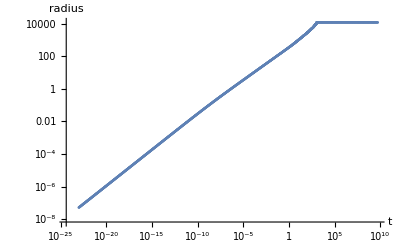

```mathematica
ListLogLogPlot[Transpose[{t,r}],AxesLabel->{"t","radius"}]
```

Fr_list[6].w

NumericArray[…]

```mathematica
w=%
```

NumericArray[…]

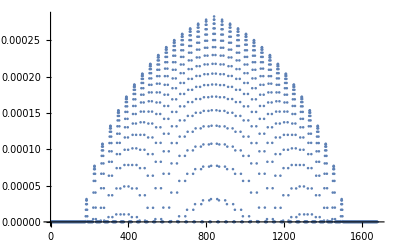

```mathematica
ListPlot[w]
```